结果表:

角度 | Wexp | Wexp0 | Wth | Wth0
90 | 0.00381022 | 1. | 0.952413 | 1.
120 | 0.00392515 | 1.03017 | 0.98462 | 1.03382
150 | 0.00424213 | 1.11336 | 1.06396 | 1.11712
180 | 0.00442413 | 1.16112 | 1.1111 | 1.16662

图像:

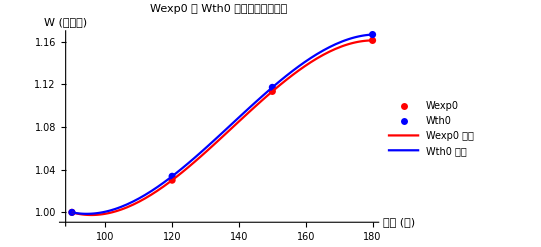

```mathematica
(*定义数据*)N1={32209,32172,32679,32722}-1217;
N2={24734,24733,24899,24625}-828;
NC=72.5*62.5*{623,641,709,732};
angles={90,120,150,180};(*角度*)
(*计算 Wexp*)
Wexp=N[NC/(N1*N2)];

(*计算勒让德多项式*)
P2[x_]:=LegendreP[2,x];
P4[x_]:=LegendreP[4,x];

(*计算 Wth*)
thetaRad=angles*Degree;(*将角度转换为弧度*)cosTheta=Cos[thetaRad];
Wth=1+0.1020*P2[#]+0.0091*P4[#]&/@cosTheta;

(*计算归一化的 Wexp0 和 Wth0*)
Wexp0=N[Wexp/Wexp[[1]]];
Wth0=N[Wth/Wth[[1]]];

(*样条拟合*)
splineWexp0=Interpolation[Transpose[{angles,Wexp0}],Method->"Spline"];
splineWth0=Interpolation[Transpose[{angles,Wth0}],Method->"Spline"];

(*列出结果表*)
resultTable=TableForm[Transpose[{angles,Wexp,Wexp0,Wth,Wth0}],TableHeadings->{None,{"角度","Wexp","Wexp0","Wth","Wth0"}}];

(*绘制图像*)
plot=Show[ListPlot[{Transpose[{angles,Wexp0}],Transpose[{angles,Wth0}]},PlotStyle->{Red,Blue},AxesLabel->{"角度 (度)","W (归一化)"},PlotLegends->{"Wexp0","Wth0"},PlotLabel->"Wexp0 和 Wth0 随角度变化的图像"],Plot[{splineWexp0[x],splineWth0[x]},{x,Min[angles],Max[angles]},PlotStyle->{Red,Blue},PlotLegends->{"Wexp0 拟合","Wth0 拟合"}]];

(*输出结果*)
Print["结果表: "];
Print[resultTable];
Print["图像: "];
plot
```

```mathematica
Aexp=(Wexp0[[4]]-Wexp0[[1]])/Wexp0[[1]]
Ath=(Wth[[4]]-Wth[[1]])/Wth[[1]]
```

0.16674

0.166616

```mathematica
(*定义数据*)N1={32209,32172,32679,32722}-1217;
N2={24734,24733,24899,24625}-828;
NC=72.5*62.5*{623,641,709,732};
angles={90,120,150,180};(*角度*)
(*计算 Wexp*)
Wexp=N[NC/(N1*N2)];

(*计算勒让德多项式*)
P2[x_]:=LegendreP[2,x];
P4[x_]:=LegendreP[4,x];

(*计算 Wth*)
thetaRad=angles*Degree;(*将角度转换为弧度*)cosTheta=Cos[thetaRad];
Wth=1+0.1020*P2[#]+0.0091*P4[#]&/@cosTheta;

(*计算归一化的 Wexp0 和 Wth0*)
Wexp0=N[Wexp/Wexp[[1]]];
Wth0=N[Wth/Wth[[1]]];

(*样条拟合*)
splineWexp0=Interpolation[Transpose[{angles,Wexp0}],Method->"Spline"];
splineWth0=Interpolation[Transpose[{angles,Wth0}],Method->"Spline"];

(*列出结果表*)
resultTable=TableForm[Transpose[{angles,Wexp,Wexp0,Wth,Wth0}],TableHeadings->{None,{"角度","Wexp","Wexp0","Wth","Wth0"}}];

(*绘制图像*)
plot=Show[ListPlot[{Transpose[{angles,Wexp0}],Transpose[{angles,Wth0}]},PlotStyle->{Red,Blue},AxesLabel->{"角度 (度)","W (归一化)"},PlotLegends->{"Wexp0","Wth0"},PlotLabel->"Wexp0 和 Wth0 随角度变化的图像"],Plot[{splineWexp0[x],splineWth0[x]},{x,Min[angles],Max[angles]},PlotStyle->{Red,Blue},PlotLegends->{"Wexp0 拟合","Wth0 拟合"}]];

(*绘制 Wth 和 Wexp 关于角度的图像*)
plotWexp=Show[ListPlot[Transpose[angles,Wexp]],PlotStyle->{Red,Blue},AxesLabel->{"角度 (度)","W"},PlotLegends->{"Wexp"},PlotLabel->"Wexp随角度变化的图像"],Plot[{splineWexp0[x]},{x,Min[angles],Max[angles]},PlotStyle->{Red},PlotLegends->{"Wexp 拟合"}]];
plotWth=Show[ListPlot[Transpose[{angles,Wth}],PlotStyle->{Blue},AxesLabel->{"角度 (度)","W"},PlotLegends->{"Wth"},PlotLabel->"Wth 随角度变化的图像"],Plot[{splineWth0[x]},{x,Min[angles],Max[angles]},PlotStyle->{Blue},PlotLegends->{"Wth 拟合"}]];

(*输出结果*)
Print["结果表: "];
Print[resultTable];
Print["Wexp0 和 Wth0 图像: "];
Print[plot];
Print["Wexp 和 Wth 图像: "];
plotWexp
plotWth
```

结果表:

角度 | Wexp | Wexp0 | Wth | Wth0
90 | 0.00381022 | 1. | 0.952413 | 1.
120 | 0.00392515 | 1.03017 | 0.98462 | 1.03382
150 | 0.00424213 | 1.11336 | 1.06396 | 1.11712
180 | 0.00442413 | 1.16112 | 1.1111 | 1.16662

Wexp0 和 Wth0 图像:

-Graphics-

Wexp 图像:

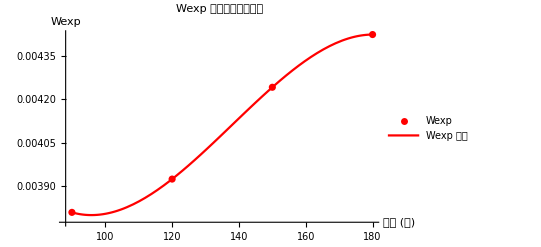

Wth 图像:

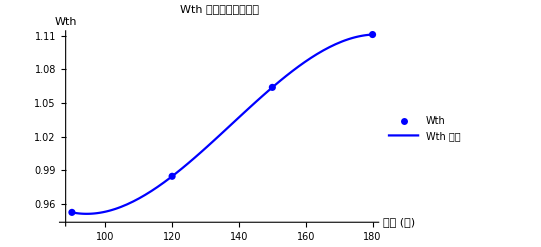

0.161122

0.166616

```mathematica
(*定义数据*)N1={32209,32172,32679,32722}-1217;
N2={24734,24733,24899,24625}-828;
NC=72.5*62.5*{623,641,709,732};
angles={90,120,150,180};(*角度*)(*计算 Wexp*)Wexp=N[NC/(N1*N2)];

(*计算勒让德多项式*)
P2[x_]:=LegendreP[2,x];
P4[x_]:=LegendreP[4,x];

(*计算 Wth*)
thetaRad=angles*Degree;(*将角度转换为弧度*)cosTheta=Cos[thetaRad];
Wth=1+0.1020*P2[#]+0.0091*P4[#]&/@cosTheta;

(*计算归一化的 Wexp0 和 Wth0*)
Wexp0=N[Wexp/Wexp[[1]]];
Wth0=N[Wth/Wth[[1]]];

(*样条拟合*)
splineWexp=Interpolation[Transpose[{angles,Wexp}],Method->"Spline"];
splineWth=Interpolation[Transpose[{angles,Wth}],Method->"Spline"];
splineWexp0=Interpolation[Transpose[{angles,Wexp0}],Method->"Spline"];
splineWth0=Interpolation[Transpose[{angles,Wth0}],Method->"Spline"];

(*列出结果表*)
resultTable=TableForm[Transpose[{angles,Wexp,Wexp0,Wth,Wth0}],TableHeadings->{None,{"角度","Wexp","Wexp0","Wth","Wth0"}}];

(*绘制 Wexp0 和 Wth0 随角度变化的图像*)
plot=Show[ListPlot[{Transpose[{angles,Wexp0}],Transpose[{angles,Wth0}]},PlotStyle->{Red,Blue},AxesLabel->{"角度 (度)","W (归一化)"},PlotLegends->{"Wexp0","Wth0"},PlotLabel->"Wexp0 和 Wth0 随角度变化的图像"],Plot[{splineWexp0[x],splineWth0[x]},{x,Min[angles],Max[angles]},PlotStyle->{Red,Blue},PlotLegends->{"Wexp0 拟合","Wth0 拟合"}]];

(*绘制 Wexp 随角度变化的图像*)
plotWexp=Show[ListPlot[Transpose[{angles,Wexp}],PlotStyle->{Red},AxesLabel->{"角度 (度)","Wexp"},PlotLegends->{"Wexp"},PlotLabel->"Wexp 随角度变化的图像"],Plot[{splineWexp[x]},{x,Min[angles],Max[angles]},PlotStyle->{Red},PlotLegends->{"Wexp 拟合"}]];

(*绘制 Wth 随角度变化的图像*)
plotWth=Show[ListPlot[Transpose[{angles,Wth}],PlotStyle->{Blue},AxesLabel->{"角度 (度)","Wth"},PlotLegends->{"Wth"},PlotLabel->"Wth 随角度变化的图像"],Plot[{splineWth[x]},{x,Min[angles],Max[angles]},PlotStyle->{Blue},PlotLegends->{"Wth 拟合"}]];

(*输出结果*)
Print["结果表: "];
Print[resultTable];
Print["Wexp0 和 Wth0 图像: "];
Print[plot];
Print["Wexp 图像: "];
Print[plotWexp];
Print["Wth 图像: "];
plotWth
Aexp=(Wexp0[[4]]-Wexp0[[1]])/Wexp0[[1]]
Ath=(Wth[[4]]-Wth[[1]])/Wth[[1]]
```